# Lección 3 - Programación funcional

## Aplicar funciones repetidamente

Anidamiento simbolico

```mathematica
NestList[f,x,4]
```

{x,f[x],f[f[x]],f[f[f[x]]],f[f[f[f[x]]]]}

```mathematica
NestList[Framed,x,5]
```

{x,x,x,x,x,x}

```mathematica
Nest[Framed,x,5]
```

Anidamiento con funciones puras

```mathematica
NestList[EdgeDetect, -Graphics-, 6]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
NestList[ColorNegate[EdgeDetect[#]] &, -Graphics-, 6]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
NestList[Blend[{#,Yellow}]&,Red,20]
```

{RGBColor[1, 0, 0],RGBColor[1, Rational[1, 2], 0],RGBColor[1, Rational[3, 4], 0],RGBColor[1, Rational[7, 8], 0],RGBColor[1, Rational[15, 16], 0],RGBColor[1, Rational[31, 32], 0],RGBColor[1, Rational[63, 64], 0],RGBColor[1, Rational[127, 128], 0],RGBColor[1, Rational[255, 256], 0],RGBColor[1, Rational[511, 512], 0],RGBColor[1, Rational[1023, 1024], 0],RGBColor[1, Rational[2047, 2048], 0],RGBColor[1, Rational[4095, 4096], 0],RGBColor[1, Rational[8191, 8192], 0],RGBColor[1, Rational[16383, 16384], 0],RGBColor[1, Rational[32767, 32768], 0],RGBColor[1, Rational[65535, 65536], 0],RGBColor[1, Rational[131071, 131072], 0],RGBColor[1, Rational[262143, 262144], 0],RGBColor[1, Rational[524287, 524288], 0],RGBColor[1, Rational[1048575, 1048576], 0]}

Anidamiento con operaciones aritméticas

```mathematica
NestList[#+1&,1,15]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}

```mathematica
NestList[2*#&,1,15]
```

{1,2,4,8,16,32,64,128,256,512,1024,2048,4096,8192,16384,32768}

```mathematica
NestList[#^2&,2,6]
```

{2,4,16,256,65536,4294967296,18446744073709551616}

Golden Ratio

```mathematica
NestList[Sqrt[1+#]&,1,5]
```

{1,√2,√(1+√2),√(1+√(1+√2)),√(1+√(1+√(1+√2))),√(1+√(1+√(1+√(1+√2))))}

```mathematica
NestList[Sqrt[1+#]&,1,10]//N
```

{1.,1.41421,1.55377,1.59805,1.61185,1.61612,1.61744,1.61785,1.61798,1.61802,1.61803}

Random Walk

```mathematica
NestList[#+RandomChoice[{+1,-1}]&,0,20]
```

{0,-1,0,-1,0,-1,-2,-1,0,-1,0,1,0,1,0,-1,-2,-1,-2,-3,-2}

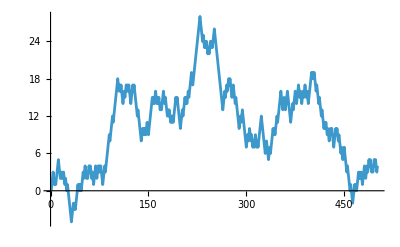

```mathematica
ListLinePlot[NestList[#+RandomChoice[{+1,-1}]&,0,500]]
```

Recursión

```mathematica
NestList[f[#]&,x,3]
```

{x,f[x],f[f[x]],f[f[f[x]]]}

```mathematica
NestList[f[#,#]&,x,3]
```

{x,f[x,x],f[f[x,x],f[x,x]],f[f[f[x,x],f[x,x]],f[f[x,x],f[x,x]]]}

```mathematica
NestList[Framed[f[#,#]]&,x,3]
```

{x,f[x,x],f[f[x,x],f[x,x]],f[f[f[x,x],f[x,x]],f[f[x,x],f[x,x]]]}

```mathematica
NestList[Framed[Column[{#,#}]]&,x,3]
```

{x,x
x,x
x
x
x,x
x
x
x
x
x
x
x}

```mathematica
NestList[Framed[Grid[{{#,#},{#,#}}]]&,x,3]
```

{x,x | x
x | x,x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x,x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x | x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x | x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x}

```mathematica
NestList[Framed[Grid[{{0,#},{#,#}}]]&,x,3]
```

{x,0 | x
x | x,0 | 0 | x
x | x
0 | x
x | x | 0 | x
x | x,0 | 0 | 0 | x
x | x
0 | x
x | x | 0 | x
x | x
0 | 0 | x
x | x
0 | x
x | x | 0 | x
x | x | 0 | 0 | x
x | x
0 | x
x | x | 0 | x
x | x}

```mathematica
NestList[Flatten[{#,Rotate[#,90 °],Rotate[#,270 °]}]&,"R",4]
```

{R,{R,R,R},{R,R,R,{R,R,R},{R,R,R}},{R,R,R,{R,R,R},{R,R,R},{R,R,R,{R,R,R},{R,R,R}},{R,R,R,{R,R,R},{R,R,R}}},{R,R,R,{R,R,R},{R,R,R},{R,R,R,{R,R,R},{R,R,R}},{R,R,R,{R,R,R},{R,R,R}},{R,R,R,{R,R,R},{R,R,R},{R,R,R,{R,R,R},{R,R,R}},{R,R,R,{R,R,R},{R,R,R}}},{R,R,R,{R,R,R},{R,R,R},{R,R,R,{R,R,R},{R,R,R}},{R,R,R,{R,R,R},{R,R,R}}}}}

Triángulo de Pascal

```mathematica
NestList[Join[{0},#]+Join[#,{0}]&,{1},5]
```

{{1},{1,1},{1,2,1},{1,3,3,1},{1,4,6,4,1},{1,5,10,10,5,1}}

```mathematica
NestList[Join[{0},#]+Join[#,{0}]&,{1},8]//Grid
```

1 |  |  |  |  |  |  |  | 
1 | 1 |  |  |  |  |  |  | 
1 | 2 | 1 |  |  |  |  |  | 
1 | 3 | 3 | 1 |  |  |  |  | 
1 | 4 | 6 | 4 | 1 |  |  |  | 
1 | 5 | 10 | 10 | 5 | 1 |  |  | 
1 | 6 | 15 | 20 | 15 | 6 | 1 |  | 
1 | 7 | 21 | 35 | 35 | 21 | 7 | 1 | 
1 | 8 | 28 | 56 | 70 | 56 | 28 | 8 | 1

## Más sobre funciones puras

Tablas de multiplicación

```mathematica
Array[f,10]
```

{f[1],f[2],f[3],f[4],f[5],f[6],f[7],f[8],f[9],f[10]}

```mathematica
Array[#^2&,10]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Table[n^2,{n,10}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Array[f,{3,4}]
```

{{f[1,1],f[1,2],f[1,3],f[1,4]},{f[2,1],f[2,2],f[2,3],f[2,4]},{f[3,1],f[3,2],f[3,3],f[3,4]}}

```mathematica
Array[f,{3,4}]//Grid
```

f[1,1] | f[1,2] | f[1,3] | f[1,4]
f[2,1] | f[2,2] | f[2,3] | f[2,4]
f[3,1] | f[3,2] | f[3,3] | f[3,4]

```mathematica
Grid[Array[Times,{5,5}]]
```

1 | 2 | 3 | 4 | 5
2 | 4 | 6 | 8 | 10
3 | 6 | 9 | 12 | 15
4 | 8 | 12 | 16 | 20
5 | 10 | 15 | 20 | 25

Funciones puras con varios argumentos

```mathematica
(f[#1,#2]&)[55,66]
```

f[55,66]

```mathematica
f[#2,#1,{#2,#2,#1}]&[55,66]
```

f[66,55,{66,66,55}]

```mathematica
Times[#1,#2]&[2,3]
```

6

Analogía:

```mathematica
f@@{55,66}
```

f[55,66]

```mathematica
Times[#1,#2]&@@{2,3}
```

6

```mathematica
Times@@{2,3}
```

6

Tabla de multilpicación con funciones puras

```mathematica
Array[#1*#2&,{5,5}]//Grid
```

1 | 2 | 3 | 4 | 5
2 | 4 | 6 | 8 | 10
3 | 6 | 9 | 12 | 15
4 | 8 | 12 | 16 | 20
5 | 10 | 15 | 20 | 25

```mathematica
Array[If[#1==#2,x,#1*#2]&,{5,5}]//Grid
```

x | 2 | 3 | 4 | 5
2 | x | 6 | 8 | 10
3 | 6 | x | 12 | 15
4 | 8 | 12 | x | 20
5 | 10 | 15 | 20 | x

Análogo:

```mathematica
Table[If[i==j,x,i*j],{i,5},{j,5}]//Grid
```

x | 2 | 3 | 4 | 5
2 | x | 6 | 8 | 10
3 | 6 | x | 12 | 15
4 | 8 | 12 | x | 20
5 | 10 | 15 | 20 | x

FoldList

```mathematica
NestList[f,x,5]
```

{x,f[x],f[f[x]],f[f[f[x]]],f[f[f[f[x]]]],f[f[f[f[f[x]]]]]}

```mathematica
NestList[Framed,x,5]
```

{x,x,x,x,x,x}

```mathematica
FoldList[f,x,{1,2,3,4,5}]
```

{x,f[x,1],f[f[x,1],2],f[f[f[x,1],2],3],f[f[f[f[x,1],2],3],4],f[f[f[f[f[x,1],2],3],4],5]}

```mathematica
FoldList[Framed[f[#1,#2]]&,x,{1,2,3,4,5}]
```

{x,f[x,1],f[f[x,1],2],f[f[f[x,1],2],3],f[f[f[f[x,1],2],3],4],f[f[f[f[f[x,1],2],3],4],5]}

Sumar con FoldList

```mathematica
FoldList[#1+#2&,0,{1,1,1,2,0,0}]
```

{0,1,2,3,5,5,5}

Lo que sucede paso a paso:

```mathematica
{0,0+1,(0+1)+1,((0+1)+1)+1,(((0+1)+1)+1)+2,((((0+1)+1)+1)+2)+0,(((((0+1)+1)+1)+2)+0)+0}
```

{0,1,2,3,5,5,5}

```mathematica
{0,0+1,0+1+1,0+1+1+1,0+1+1+1+2,0+1+1+1+2+0,0+1+1+1+2+0+0}
```

{0,1,2,3,5,5,5}

```mathematica
FoldList[#1+#2&,0,{a,b,c,d,e}]
```

{0,a,a+b,a+b+c,a+b+c+d,a+b+c+d+e}

```mathematica
FoldList[Plus,0,{a,b,c,d,e}]
```

{0,a,a+b,a+b+c,a+b+c+d,a+b+c+d+e}

Reconstruir números

```mathematica
FoldList[10 #1+#2&,{8,7,6,1,2,3,9,8,7}]
```

{8,87,876,8761,87612,876123,8761239,87612398,876123987}

Incorporar imagenes

```mathematica
FoldList[ImageAdd,
 {-Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Reorganizando listas

Transpose

```mathematica
Transpose[{{1,2},{3,4},{5,6},{7,8},{9,10}}]
```

{{1,3,5,7,9},{2,4,6,8,10}}

Transpose the pair of lists back to a list of pairs:

```mathematica
Transpose[{{1,3,5,7,9},{2,4,6,8,10}}]
```

{{1,2},{3,4},{5,6},{7,8},{9,10}}

Thread

```mathematica
Thread[{1,3,5,7,9}->{2,4,6,8,10}]
```

{1→2,3→4,5→6,7→8,9→10}

Partition

```mathematica
Partition[Range[12],3]
```

{{1,2,3},{4,5,6},{7,8,9},{10,11,12}}

```mathematica
Grid[Partition[Characters["An array of text made in the Wolfram Language"],9],Frame->All]
```

A | n |   | a | r | r | a | y |  
o | f |   | t | e | x | t |   | m
a | d | e |   | i | n |   | t | h
e |   | W | o | l | f | r | a | m
  | L | a | n | g | u | a | g | e

Partition con offset

```mathematica
Partition[Range[10],3,1]
```

{{1,2,3},{2,3,4},{3,4,5},{4,5,6},{5,6,7},{6,7,8},{7,8,9},{8,9,10}}

```mathematica
Grid[Partition[Characters["Wolfram Language"],12,1],Frame->All]
```

W | o | l | f | r | a | m |   | L | a | n | g
o | l | f | r | a | m |   | L | a | n | g | u
l | f | r | a | m |   | L | a | n | g | u | a
f | r | a | m |   | L | a | n | g | u | a | g
r | a | m |   | L | a | n | g | u | a | g | e

```mathematica
Grid[Partition[Characters["Wolfram Language"],12,2],Frame->All]
```

W | o | l | f | r | a | m |   | L | a | n | g
l | f | r | a | m |   | L | a | n | g | u | a
r | a | m |   | L | a | n | g | u | a | g | e

Flatten

```mathematica
IntegerDigits/@Range[20]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{1,0},{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{2,0}}

```mathematica
Flatten[IntegerDigits/@Range[20]]
```

{1,2,3,4,5,6,7,8,9,1,0,1,1,1,2,1,3,1,4,1,5,1,6,1,7,1,8,1,9,2,0}

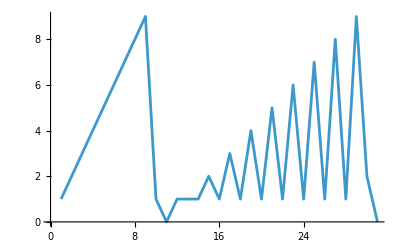

```mathematica
ListLinePlot[Flatten[IntegerDigits/@Range[20]]]
```

Flatten con niveles

```mathematica
Table[IntegerDigits[i^j],{i,4},{j,4}]
```

{{{1},{1},{1},{1}},{{2},{4},{8},{1,6}},{{3},{9},{2,7},{8,1}},{{4},{1,6},{6,4},{2,5,6}}}

```mathematica
Flatten[Table[IntegerDigits[i^j],{i,4},{j,4}]]
```

{1,1,1,1,2,4,8,1,6,3,9,2,7,8,1,4,1,6,6,4,2,5,6}

```mathematica
Flatten[Table[IntegerDigits[i^j],{i,4},{j,4}],1]
```

{{1},{1},{1},{1},{2},{4},{8},{1,6},{3},{9},{2,7},{8,1},{4},{1,6},{6,4},{2,5,6}}

Split

```mathematica
Split[{1,1,1,2,2,1,1,3,1,1,1,2}]
```

{{1,1,1},{2,2},{1,1},{3},{1,1,1},{2}}

Gather

```mathematica
Gather[{1,1,1,2,2,1,1,3,1,1,1,2}]
```

{{1,1,1,1,1,1,1,1},{2,2,2},{3}}

GatherBy

```mathematica
GatherBy[Characters["It's true that 2+2 is equal to 4!"],LetterQ]
```

{{I,t,s,t,r,u,e,t,h,a,t,i,s,e,q,u,a,l,t,o},{', , , ,2,+,2, , , , ,4,!}}

Sort & SortBy

```mathematica
Sort[Table[IntegerDigits[2^n],{n,10}]]
```

{{2},{4},{8},{1,6},{3,2},{6,4},{1,2,8},{2,5,6},{5,1,2},{1,0,2,4}}

```mathematica
SortBy[Table[IntegerDigits[2^n],{n,10}],First]
```

{{1,6},{1,2,8},{1,0,2,4},{2},{2,5,6},{3,2},{4},{5,1,2},{6,4},{8}}

Teoria de Conjuntos

```mathematica
Union[{1,9,5,3,1,4,3,1,3,3,5,3,9}]
```

{1,3,4,5,9}

```mathematica
Union[{2,1,3,7,9},{4,5,1,2,3,3},{3,1,2,8,5}]
```

{1,2,3,4,5,7,8,9}

```mathematica
Intersection[{2,1,3,7,9},{4,5,1,2,3,3},{3,1,2,8}]
```

{1,2,3}

```mathematica
Complement[{4,5,1,2,3,3},{3,1,2,8}]
```

{4,5}

```mathematica
Union[Alphabet["English"],Alphabet["Swedish"],Alphabet["Turkish"]]
```

{ğ,ş,a,å,ä,b,c,ç,d,e,f,g,h,i,ı,j,k,l,m,n,o,ö,p,q,r,s,t,u,ü,v,w,x,y,z}

```mathematica
Complement[Alphabet["Swedish"],Alphabet["English"]]
```

{å,ä,ö}

Riffle

```mathematica
Riffle[{1,2,3,4,5},x]
```

{1,x,2,x,3,x,4,x,5}

```mathematica
Riffle[Characters["WOLFRAM"],"--"]
```

{W,--,O,--,L,--,F,--,R,--,A,--,M}

```mathematica
StringJoin[Riffle[Characters["WOLFRAM"],"--"]]
```

W--O--L--F--R--A--M

Permutations & Subsets

```mathematica
Permutations[{Red,Green,Blue}]
```

{{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]},{RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 1, 0]},{RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1]},{RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0]},{RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 1, 0]},{RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[1, 0, 0]}}

```mathematica
Subsets[{Red,Green,Blue}]
```

{{},{RGBColor[1, 0, 0]},{RGBColor[0, 1, 0]},{RGBColor[0, 0, 1]},{RGBColor[1, 0, 0],RGBColor[0, 1, 0]},{RGBColor[1, 0, 0],RGBColor[0, 0, 1]},{RGBColor[0, 1, 0],RGBColor[0, 0, 1]},{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]}}

Tuples

```mathematica
Tuples[{Red,Green},3]
```

{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0]},{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0]},{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0]},{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0]},{RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0]},{RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0]},{RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0]},{RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0]}}

## Expresiones y su estructura

Expresión simbólica sin ningún significado particular asociado:

```mathematica
f[x,y]
```

f[x,y]

```mathematica
List[x,y,z]
```

{x,y,z}

```mathematica
List[List[a,b],List[c,d]]
```

{{a,b},{c,d}}

Estructura interna

```mathematica
FullForm[{{a,b},{c,d}}]
```

List[List[a,b],List[c,d]]



```mathematica
Graphics[Circle[{0,0}]]
```

```mathematica
FullForm[-Graphics-]
```

Graphics[Circle[List[0,0]]]

Expresiones simbolicas evaluadas

```mathematica
Plus[2,2]
```

4

```mathematica
{Plus[3,3],Times[3,3],Power[3,3]}
```

{6,9,27}

```mathematica
{Plus[3,3],Times[3,3],Power[3,3]}//FullForm
```

List[6,9,27]

```mathematica
Blur[-Graphics-, 5]
```

-Graphics-

```mathematica
Blur[Graphics[Circle[{0,0}]],5]
```

-Graphics-

Atoms: Bloques fundamentales

```mathematica
x
```

x

```mathematica
x+x+x+2 y+y+x
```

4 x+3 y

Estructura de una expresión

```mathematica
ExpressionTree[{f[x,f[x,y]],{x,y,f[1]}}]
```

-Graphics-

```mathematica
ExpressionTree[Graphics[{Circle[{0,0}],Hue[0.5],Disk[{1,1}]}]]
```

-Graphics-

Estructura uniforme

```mathematica
List[x,y,z][[2]]
```

y

```mathematica
f[x,y,z][[2]]
```

y

```mathematica
Graphics[Circle[{0,0}]][[1]]
```

Circle[{0,0}]

```mathematica
Graphics[Circle[{0,0}]][[1,1]]
```

{0,0}

```mathematica
-Graphics-[[1, 1]]
```

{0,0}

Cabeceras  (Head)

```mathematica
Head[{x,y,z}]
```

List

```mathematica
Head[1234]
```

Integer

```mathematica
Head[12.45]
```

Real

```mathematica
Head["hello"]
```

String

```mathematica
Head[x]
```

Symbol

Patrones

```mathematica
Cases[{x,y,3,4,z,6,7},_Integer]
```

{3,4,6,7}

```mathematica
Cases[{99,x,y,z,101,102},n_Integer->{n,n}]
```

{{99,99},{101,101},{102,102}}

Forma de operador

```mathematica
FullForm[#^2&]
```

Function[Power[Slot[1],2]]

```mathematica
Function[Power[Slot[1],2]][1000]
```

1000000

```mathematica
Select[#>4&][{1,2.2,3,4.5,5,6,7.5,8}]
```

{4.5,5,6,7.5,8}

```mathematica
Cases[_Integer]@Select[#>4&]@{1,2.2,3,4.5,5,6,7.5,8}
```

{5,6,8}

Operaciones estructurales

```mathematica
Length[f[x,y,z]]
```

3

```mathematica
f/@g[x,y,z]
```

g[f[x],f[y],f[z]]

```mathematica
f@@{x,y,z}
```

f[x,y,z]

```mathematica
Plus@@{1,1,1,1}
```

4

```mathematica
#1->#2&@@{x,y}
```

x→y

```mathematica
Rule@@{x,y}
```

x→y

```mathematica
f@@@{{1,2,3},{4,5,6}}
```

{f[1,2,3],f[4,5,6]}

```mathematica
Rule@@@{{1,10},{2,20},{3,30}}
```

{1→10,2→20,3→30}

Aplicacion del MapApply

```mathematica
Partition[Characters["antidisestablishmentarianism"],2,1]
```

{{a,n},{n,t},{t,i},{i,d},{d,i},{i,s},{s,e},{e,s},{s,t},{t,a},{a,b},{b,l},{l,i},{i,s},{s,h},{h,m},{m,e},{e,n},{n,t},{t,a},{a,r},{r,i},{i,a},{a,n},{n,i},{i,s},{s,m}}

```mathematica
Rule@@@Partition[Characters["antidisestablishmentarianism"],2,1]
```

{a→n,n→t,t→i,i→d,d→i,i→s,s→e,e→s,s→t,t→a,a→b,b→l,l→i,i→s,s→h,h→m,m→e,e→n,n→t,t→a,a→r,r→i,i→a,a→n,n→i,i→s,s→m}

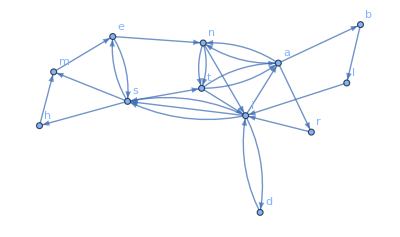

```mathematica
Graph[Rule@@@Partition[Characters["antidisestablishmentarianism"],2,1],VertexLabels->All]
```